## LIBR

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## APPLICATIONS

## tmp-movie_protocol_IN-DEV

```mathematica
(*
Table[gLine[{k,If[k<=10,k,11-Mod[k,10]]},Color->Cyan,Thickness->0.0025],{k,2,19}]//toGL//gr
 f[x_,y_]:=Table[gLine[{x,y},pGon[128][[k]],Color->Gray,Thickness->0.0025],{k,1,128}]//toGL//gr
f[-0.5,-0.5]
gAnimation=ConstantArray[0,101]
Table[{k,k},{k,-0.5,0.5,0.01}]//Length
For[k=1,k<=101,k++,gAnimation[[k]]=f[-0.51+ k/100,-0.51+ k/100]]
Export["movie.avi",gAnimation]
*)
```

## DEV

## Three Reflections Theorem

### Introduction

-Graphics-

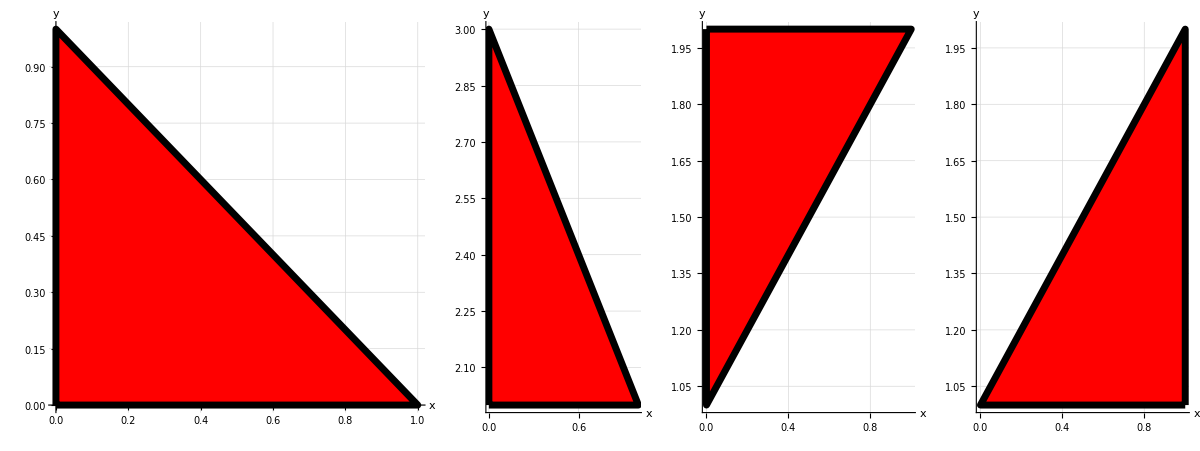

```mathematica
GraphicsRow[
{
gPolygon[{{0,0},{1,0},{0,1}}]//toGL//gr1,
tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}]//toGL//gr1,
rot3[tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}],{3/2Pi/1,{0,2}}]//toGL//gr1,
ref3[rot3[tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}],{3/2Pi/1,{0,2}}],{{-1,1},{0,1}}]//toGL//gr1
}
]
```

### Translation :> Reflections

```mathematica
traM:={{1,0,0},{0,1,2},{0,0,1}}
ptsM:={{0,1,0},{0 ,0,1},{1,1,1}}

traM//mf
ptsM//mf
```

(1 | 0 | 0
0 | 1 | 2
0 | 0 | 1)

(0 | 1 | 0
0 | 0 | 1
1 | 1 | 1)

```mathematica
traM.ptsM//mf
```

(0 | 1 | 0
2 | 2 | 3
1 | 1 | 1)

### tmp

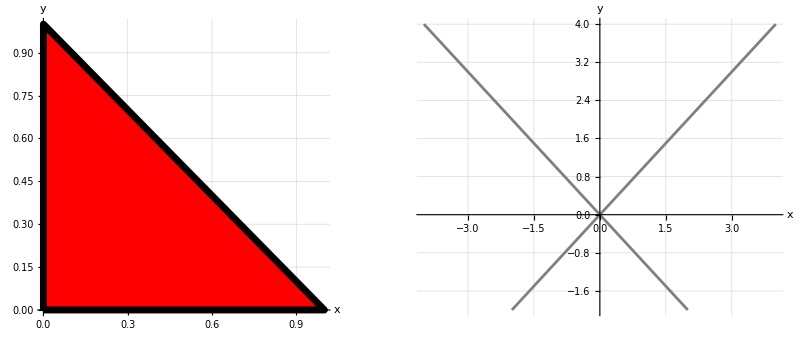

```mathematica
GraphicsRow[
{
gPolygon[{{0,0},{1,0},{0,1}}]//toGL//gr1,
{
gLine[{-2,-2},{4,4},Color->Gray, Thickness->0.005]//toGL,
gLine[{2,-2},{-4,4},Color->Gray, Thickness->0.005]//toGL}//gr1
}
]
```